```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

# Manual By Example

## 1. Defining a Complex Fan

1.1 Defining a Complex Fan in parts

First we define a magnitude interval and an angle interval like follows

```mathematica
MagnitudeInterval01= INDefine[firstExtreme->2,secondExtreme->4,feIncluded->"[",seIncluded->"]"]
```

IN[FE[2],SE[4],FEI[[],SEI[]]]

```mathematica
AngleInterval01= INDefine[firstExtreme->0,secondExtreme->90,feIncluded->"[",seIncluded->"]"]
```

IN[FE[0],SE[90],FEI[[],SEI[]]]

With the INDefine function we can define a magnitude interval or an angle interval, this function can be called with from 0 to 4 rules; we need to especify the rule for the first extreme firstExtreme->value, the rule for the second extreme secondExtreme->value, the rule to especify if the first extreme is included in the interval feIncluded->value (with “[” the extreme is included, with “(” the extreme is not included) and the rule to especify if the second extreme is included in the interval seIncluded->value (with “]“ the extreme is included, with “)“ the extreme is not included).
If we do not especify some or all rules, the INDefine function uses a value by default for each missed rule.

After defining a magnitude interval and an angle interval, we define a complex fan like follows

```mathematica
ComplexFan01=CFDefine[magnitudeInterval->MagnitudeInterval01,angleInterval->AngleInterval01]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[90],FEI[[],SEI[]]]]

With the CFDefine function we can define a complex fan, this function can be called with from 0 to 2 rules, one rule of the form magnitudeInterval->value to especify the value of the magnitude interval, another rule of the form angleInterval->value to especify the value of the angle interval; if we do not especify some or all rules, the CFDefine function uses a value by default for each missed rule.

1.2 Defining a Complex fan directly

We can reach this doing the next

```mathematica
ComplexFan02=CFDefine[magnitudeInterval->INDefine[firstExtreme->4,secondExtreme->8],angleInterval->INDefine[firstExtreme->90,secondExtreme->160]]
```

CF[IN[FE[4],SE[8],FEI[[],SEI[]]],IN[FE[90],SE[160],FEI[[],SEI[]]]]

As we can see, we only need to combine all steps from the past section.

In a Complex Fan the first interval always is the magnitude interval and the second interval is the angle interval.

1.3 Defining a Complex Fan in parts, short way

First we define a magnitude interval and an angle interval like follows

```mathematica
MagnitudeInterval02= INDefineShort["[",12,14,")"]
```

IN[FE[12],SE[14],FEI[[],SEI[)]]

```mathematica
AngleInterval02= INDefineShort["(",20,190,"]"]
```

IN[FE[20],SE[190],FEI[(],SEI[]]]

With the INDefineShort function we can define a magnitude interval or an angle interval, in a short manner, this function can be called with four arguments as we saw in the example. The first argument if the first extreme is included in the interval (with “[“ the extreme is included, with “(“ the extreme is not included), the second the value of the first extreme, the third the value of the second extreme and the last if the second extreme is included in the interval (with “]” the extreme is included, with “)” the extreme is not included).

After defining a magnitude interval and an angle interval, we define a complex fan like follows

```mathematica
ComplexFan03=CFDefine[magnitudeInterval->MagnitudeInterval02,angleInterval->AngleInterval02]
```

CF[IN[FE[12],SE[14],FEI[[],SEI[)]],IN[FE[20],SE[190],FEI[(],SEI[]]]]

1.4 Defining a Complex Fan, very short way

With the CFDefineShort function we can define a complex fan in a very short manner, this function can be called with two arguments as we will see in the next example. The first argument is a pattern of the form “MI[fei,fe,se,sei]”, where “MI” indicates that this is a magnitude interval, “fei” is about if the first extreme is included in the interval (with “[“ the extreme is included, with “(“ the extreme is not included), “fe” is the value for the first extreme, “se” is the value for the second extreme and “sei” is about if the second extreme is included in the interval (with “]” the extreme is included, with “)” the extreme is not included). The second argument is a pattern of the form “AI[fei,fe,se,sei]”, where “AI” indicates that this is an angle interval and the rest is similar to the first argument.

```mathematica
ComplexFan04=CFDefineShort[MI["[",22,44,"]"],AI["[",40,290,"]"]]
```

CF[IN[FE[22],SE[44],FEI[[],SEI[]]],IN[FE[40],SE[290],FEI[[],SEI[]]]]

When we define a complex fan the result is a pattern of the form “CF[IN[FE[fe],SE[se],FEI[fei],SEI[sei]],IN[FE[fe],SE[se],FEI[fei],SEI[sei]]]”, where ‘CF’ indicates that this is a complex fan, ‘IN’ an interval (the first ‘IN’ always represents the magnitude interval and the second the angle interval), ‘FE’ the first extreme, ‘SE’ the second extreme, ‘FEI’ if the first extreme is included in the interval and ‘SEI’ if the second extreme is included in the interval.

## 2. Representations of a Complex Fan

When we define a Complex Fan we obtain a Complex Fan in the encapsulated form, and in this form we use a complex fan to perform an operation. But we can obtain a string form of a Complex Fan or plot a Complex Fan too, when we require it.

2.1 String form of a Complex Fan

We can obtain a string representation of a Complex Fan using the function CFStringForm like this

```mathematica
CFStringForm[ComplexFan01]
```

[2,4] ∠ [0,90]

2.2 Plotting a Complex Fan

We can plot a Complex Fan using the function CFPlot, this function plots a list of complex fans, you can use it like follows

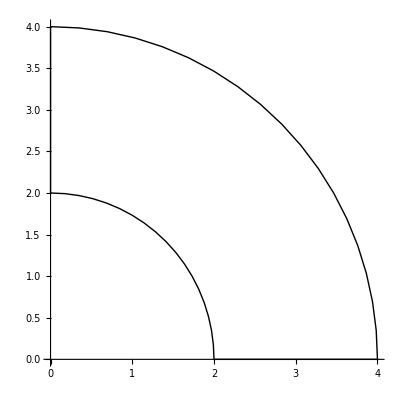

```mathematica
CFPlot[{ComplexFan01}]
```

## 3. Getting and Setting the encapsulated data in a Complex Fan

Because the information is encapsulated in a Complex Fan we need a way to get and to set that data, to achieve this we need the following getters and setters.

3.1 Getters

```mathematica
ComplexFan01
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[90],FEI[[],SEI[]]]]

To get encapsulated information of a Complex Fan we can use the following functions.

```mathematica
CFGetMI[ComplexFan01]
```

IN[FE[2],SE[4],FEI[[],SEI[]]]

With the CFGetMI function we can obtain the Magnitude Interval of a Complex Fan.

```mathematica
CFGetAI[ComplexFan01]
```

IN[FE[0],SE[90],FEI[[],SEI[]]]

With the CFGetAI function we can obtain the Angle Interval of a Complex Fan.

Similarly we can obtain the encapsulated information from an Interval with the next functions:

INGetFE - to get the first extreme of an Interval

```mathematica
INGetFE[MagnitudeInterval01]
```

2

INGetSE - to get the second extreme of an Interval

```mathematica
INGetSE[MagnitudeInterval01]
```

4

INGetFEI and INGetSEI - to get the limits of an interval

```mathematica
INGetFEI[MagnitudeInterval01]
```

[

```mathematica
INGetSEI[MagnitudeInterval01]
```

]

3.2 Setters

```mathematica
ComplexFan01
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[90],FEI[[],SEI[]]]]

To set information in a complex fan we can use the following functions.

With the CFSetMI function we can set the magnitude interval of a Complex Fan.

```mathematica
MagnitudeInterval02=INDefine[firstExtreme->5,secondExtreme->10]
```

IN[FE[5],SE[10],FEI[[],SEI[]]]

```mathematica
CFSetMI[ComplexFan01,MagnitudeInterval02]
```

```mathematica
ComplexFan01
```

CF[IN[FE[5],SE[10],FEI[[],SEI[]]],IN[FE[0],SE[90],FEI[[],SEI[]]]]

With the CFSetAI function we can set the angle interval of a Complex Fan.

```mathematica
AngleInterval02=INDefine[firstExtreme->35,secondExtreme->80,feIncluded->"(",seIncluded->")"]
```

IN[FE[35],SE[80],FEI[(],SEI[)]]

```mathematica
CFSetAI[ComplexFan01,AngleInterval02]
```

```mathematica
ComplexFan01
```

CF[IN[FE[5],SE[10],FEI[[],SEI[]]],IN[FE[35],SE[80],FEI[(],SEI[)]]]

Simirarly we can set the information in an Interval with the following functions:

INSetFE - To set the first extreme

```mathematica
INSetFE[MagnitudeInterval02,6]
```

```mathematica
MagnitudeInterval02
```

IN[FE[6],SE[10],FEI[[],SEI[]]]

INSetSE - To set the first extreme

```mathematica
INSetSE[MagnitudeInterval02,11]
```

```mathematica
MagnitudeInterval02
```

IN[FE[6],SE[11],FEI[[],SEI[]]]

INSetFEI - To set the limit of the first extreme

```mathematica
INSetFEI[MagnitudeInterval02,"("]
```

```mathematica
MagnitudeInterval02
```

IN[FE[6],SE[11],FEI[(],SEI[]]]

INSetSEI - To set the limit of the second extreme

```mathematica
INSetSEI[MagnitudeInterval02,")"]
```

```mathematica
MagnitudeInterval02
```

IN[FE[6],SE[11],FEI[(],SEI[)]]

## 4. Operations between Complex Fans

4.1 Negation

We can reach this unary operation with the function CFNegation, this function receives the complex fan that will be negated and returns it.

```mathematica
ResNeg=CFNegation[ComplexFan01]
```

CF[IN[FE[5],SE[10],FEI[[],SEI[]]],IN[FE[215],SE[260],FEI[(],SEI[)]]]

```mathematica
CFStringForm[ComplexFan01]
```

[5,10] ∠ (35,80)

```mathematica
CFStringForm[ResNeg]
```

[5,10] ∠ (215,260)

4.2 Product

We can achieve this operation between two Complex Fans with the function CFProduct, it receives two complex fans and returns the resulting complex fan.

```mathematica
ResProd=CFProduct[ComplexFan01,ComplexFan02]
```

CF[IN[FE[20],SE[80],FEI[[],SEI[]]],IN[FE[125],SE[240],FEI[(],SEI[)]]]

```mathematica
CFStringForm[ComplexFan01]
```

[5,10] ∠ (35,80)

```mathematica
CFStringForm[ComplexFan02]
```

[4,8] ∠ [90,160]

```mathematica
CFStringForm[ResProd]
```

[20,80] ∠ (125,240)

4.3 Division

We can perform this operation between two Complex Fans, with the function CFDivision, it receives two complex fans and returns the resulting complex fan.

```mathematica
ResDiv=CFDivision[ComplexFan02,ComplexFan01]
```

CF[IN[FE[0.4],SE[1.6],FEI[[],SEI[]]],IN[FE[10],SE[125],FEI[(],SEI[)]]]

```mathematica
CFStringForm[ResDiv]
```

[0.4,1.6] ∠ (10,125)

4.4 Addition

We can make it using the CFAddition function, it receives two complex fans and a flag True or False, to turn on or to turn off debugging. It returns the resulting complex fan.

```mathematica
ResAdd=CFAddition[ComplexFan01,ComplexFan02]
```

CF[IN[FE[4.24935],SE[17.9324],FEI[[],SEI[]]],IN[FE[49.9233],SE[130.959],FEI[[],SEI[]]]]

```mathematica
CFStringForm[ResAdd]
```

[4.24935,17.9324] ∠ [49.9233,130.959]

4.5 Subtraction

We can do a subtraction between two complex fans, with the function CFSubtraction, it receives two complex fans and a flag True or False, to turn on or to turn off debugging. It returns the resulting complex fan.

```mathematica
ResSub=CFSubtraction[ComplexFan02,ComplexFan01]
```

CF[IN[FE[0.868241],SE[15.9929],FEI[[],SEI[]]],IN[FE[105.763],SE[253.462],FEI[[],SEI[]]]]

```mathematica
CFStringForm[ResSub]
```

[0.868241,15.9929] ∠ [105.763,253.462]

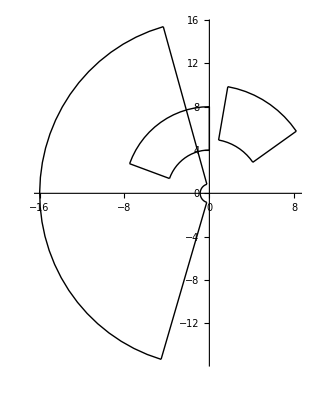

```mathematica
CFPlot[{ComplexFan02,ComplexFan01,ResSub}]
```

## 5. Plotting results

Also we can verify the correctness of our results in addition and subtraction, basiclly the most difficult operations, using the next functions.

The CFAdditionPlot function plots the addition of two complex fans, it receives the first operand of the addition, the second operand of the addition and the result of the addition, like next

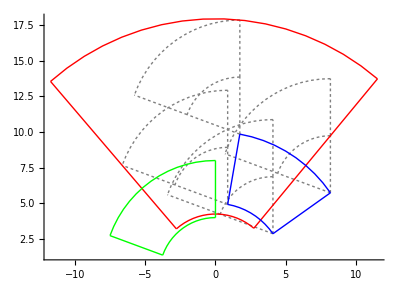
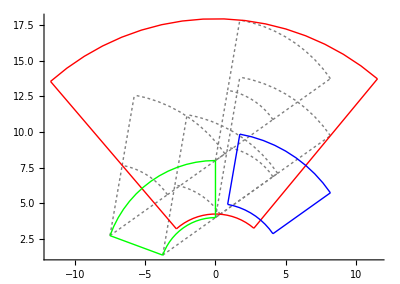

```mathematica
CFAdditionPlot[ComplexFan01,ComplexFan02,ResAdd]
```

The CFSubtractionPlot function plots the subtraction of two complex fans, it receives the first operand of the subtraction, the second operand of the subtraction and the result of the subtraction, like follows

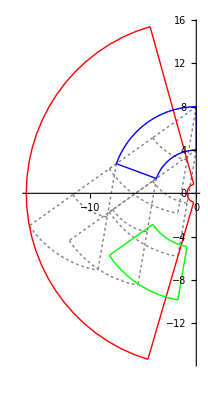
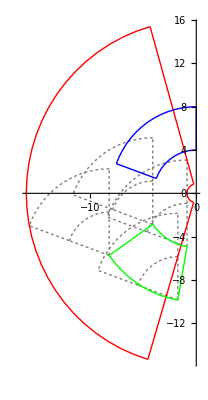

```mathematica
CFSubtractionPlot[ComplexFan02,ComplexFan01,ResSub]
```

You can notice that the CFSubtractionPlot only plots the addition from the first operand of the subtraction with the negated second operand of the subtraction.